# VYA - Přednášky

## 3. Přednáška

### Používání AI

https://chat.openai.com/

Zadání: “Prosím, napiš skript ve Wolfram Mathematica, který vygeneruje graf funkcí Sin a Cos, sinus modře a kosínus červeně, popíše osy a graf bude mít GridLines”

Odpoveď: “Samozřejmě, zde je skript ve Wolfram Mathematica, který vygeneruje graf funkcí Sin a Cos s popisem os a s GridLines:”

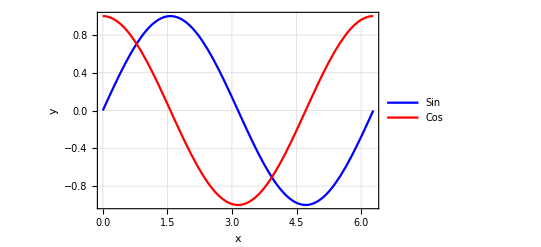

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{Style["x",Bold,14],Style["y",Bold,14]},PlotLegends->{"Sin","Cos"},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->400]
```

“Tento skript vykreslí graf funkcí Sin a Cos na intervalu [0, 2 Pi]. Sinus je vykreslen modře a kosinus červeně. Osa x je popsaná nápisem “x” a osa y nápisem “y”. Graf má také mřížky (GridLines) s šedým stylem (GridLinesStyle). Celková velikost grafu je nastavena na 400 pixelů.

Můžete tento skript spustit ve Wolfram Mathematica a zobrazí se vám výsledný graf.”

### Příkaz module

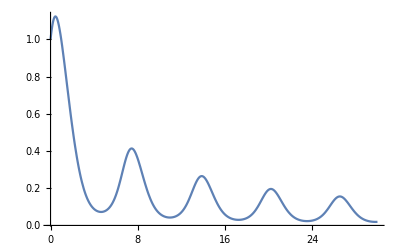

```mathematica
Quiet@Remove["Global`*"];
s[a_] := NDSolve[{y'[x] == y[x] Cos[x + a*y[x]], y[0] == 1}, y, {x, 0, 30}]
g[a_] := Plot[Evaluate[y[x] /. s[a]], {x, 0, 30}, PlotRange -> All]
g[1]
```

```mathematica
Quiet@Remove["Global`*"];
f[a_] := Module[{reseni}, reseni = NDSolve[{y'[x] == y[x]Cos[x + a*y[x]], y[0] == 1}, y, {x, 0, 30}];
	Plot[Evaluate[y[x] /. s[a]], {x, 0, 30}, PlotRange -> All]]
f[2]
```

1

### Užitečná funkce Tanh

5/2+1/2 Tanh[5 (-4+x)]

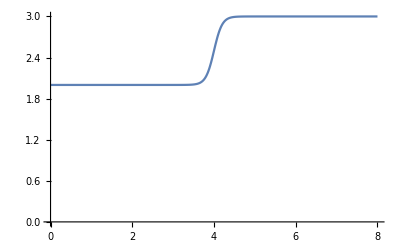

```mathematica
Quiet@Remove["Global`*"];
Prechod[Odkud_, Kam_, Zmena_, Strmost_, Promenna_] := Module[{Rovnice, a, b, Dosaz}, 
Rovnice = {a - b == Odkud, a + b == Kam};
Dosaz = Solve[Rovnice, {a, b}][[1]]; 
a+b*Tanh[Strmost*(Promenna - Zmena)] /. Dosaz];
Graf = Prechod[2, 3, 4, 5, x]
Plot[Graf, {x, 0, 8}, AxesOrigin -> {0, 0}]
```

### Pure functions

```mathematica
Quiet@Remove["Global`*"];
f[x_] := x^2;
f[5]
```

25

```mathematica
?#
```

```mathematica
#^2 & [5]
```

25

```mathematica
g[x_,y_] := x + y^2
g[E, Pi]
```

ⅇ+π^2

```mathematica
#1 + #2^2 & [E, Pi]
```

ⅇ+π^2

```mathematica
h := #1 + #2^2&
h[E, Pi]
```

ⅇ+π^2

```mathematica
?Select
```

```mathematica
Test[x_] := x > 2
Test[1]
Test[3]
Select[{1, 2, 4, 3, 7, 6, 5, 8}, Test]
```

False

True

{4,3,7,6,5,8}

```mathematica
Select[{1, 2, 4, 3, 7, 6, 5, 8}, # > 2 &]
```

{4,3,7,6,5,8}

```mathematica
# > 2 & [1]
```

False